```mathematica
m:=2.3
l:=Sqrt[8]
n:=7000
d:=3
"causal events" n
A=CSMinkowski3Diamond[l,n];
ρ:=CSize[A] / CVolume[A]
"density" ρ
Subscript[C, 1]=CausalMatrix[A];
V=(IdentityMatrix[n]+Subscript[C, 1]).(IdentityMatrix[n]+Subscript[C, 1]);

(*
L=LinkMatrix[A];(*Compute L*)
kmax=1;
While[MatrixPower[L,kmax]!=ConstantArray[0,{n,n}],kmax++];(*Find kmax*)
lengths=Table[MatrixPower[L,k],{k,1,kmax-1}];(*Compute all powers of *)

kmax "kmax"

MaxLengthMatrix=ConstantArray[0,{n,n}];
Do[pos=Position[Normal[lengths[[k]]],x_/;x>0,{2}];
Scan[Function[{ij},MaxLengthMatrix[[Sequence@@ij]]=k;],pos],
{k,1,kmax-1}];

MaxLength[i_,j_]:=MaxLengthMatrix[[i,j]];(*Find the length of the longest path from i to j (i.e the largest value of k such that L^k[[i,j]] is non-zero)*)

m3=2.19;
a=((ρ π)/12)^(1/3)m3/(2π);
K = Table[Piecewise[{{0,MaxLength[i,j]==0},{a/MaxLength[i,j],MaxLength[i,j]>0}}],{i,n},{j,n}];
*)
(*
VolTime=(12/(π ρ))^(1/3)*(V)^(1/3)*Subscript[C, 1];  
*)
K0=Table[Quiet[Check[1/(2π)((π ρ)/12)^(1/3)(V[[i,j]])^(-1/3),0]],{i,n},{j,n}];
K=K0.Inverse[IdentityMatrix[n]+m^2/ρ K0]//Chop;



Z=Table[Sqrt[(A[[1,i,1]]-A[[1,j,1]])^2+(A[[1,i,2]]-A[[1,j,2]])^2-(A[[1,i,3]]-A[[1,j,3]])^2],{i,n},{j,n}];
MfdTime=Chop[Subscript[C, 1]*Im[Z]];

points=Transpose[{Flatten[MfdTime],Flatten[K]}];
points=DeleteCases[Chop[points],{0,_}];
Length[points]"causal relations"
```

7000 causal events

1181.67 density

5635215 causal relations

```mathematica
K2=K.Inverse[IdentityMatrix[n]+m^2/ρ K];
pointsMass=Transpose[{Flatten[MfdTime],Flatten[K2]}];
pointsMass=DeleteCases[Chop[pointsMass],{0,_}];
```

```mathematica
sample:=100000
n
(*ListPlot[RandomSample[points,sample],PlotStyle->PointSize[0.00001],ImageSize->600,AxesLabel->{"Matrix 1 entries","Matrix 2 entries"}]
Plot[1/2 BesselJ[0,m*x],{x,0,l}]
*)
plot1=ListPlot[RandomSample[points,sample],PlotStyle->PointSize[0.00001],ImageSize->600,AxesLabel->{"Proper time τ","Greens function"}];
plot2=Plot[1/(2π)Cos[m x]/x,{x,0,l},PlotStyle->Red,PlotRange-> {{0,2},{-1,2}}];
Show[plot1,plot2]
```

7000

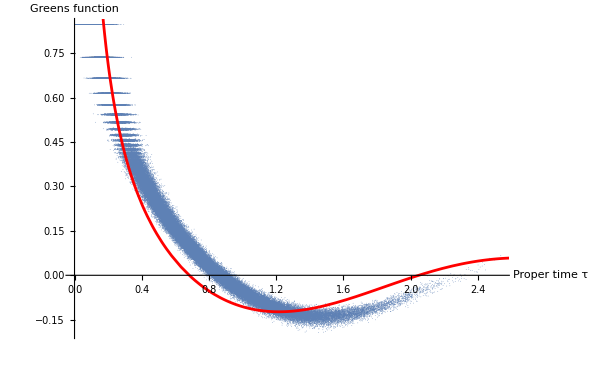
```mathematica
-Graphics-n=7000 (ρ=1181.7)
```

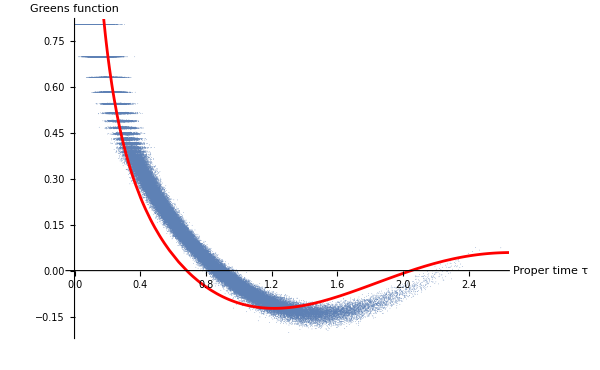
```mathematica
-Graphics-n=6000 (ρ= 1012.9)
```

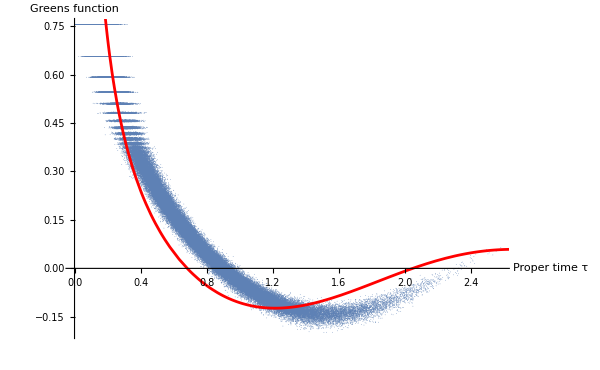
```mathematica
-Graphics-n=5000 (ρ=844)
```

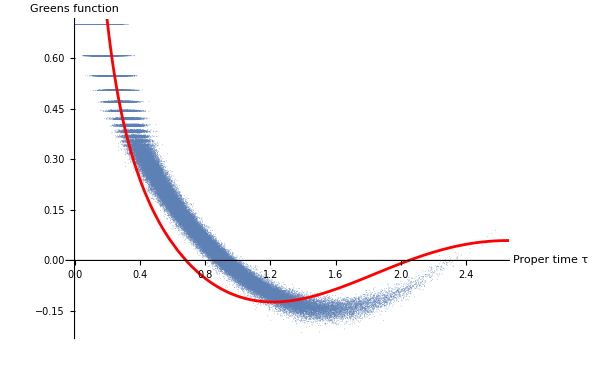
```mathematica
-Graphics-n=4000 (ρ=675.2)
```

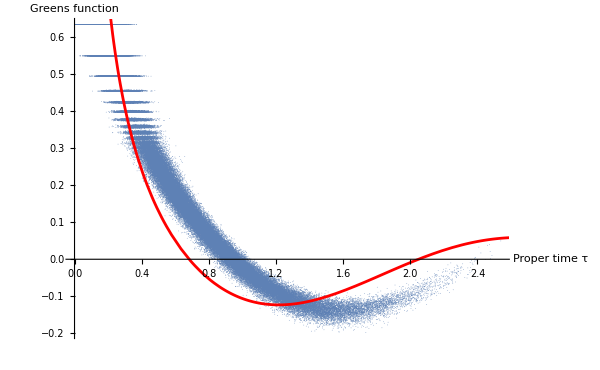
```mathematica
-Graphics-n=3000 (ρ=506.4)
```

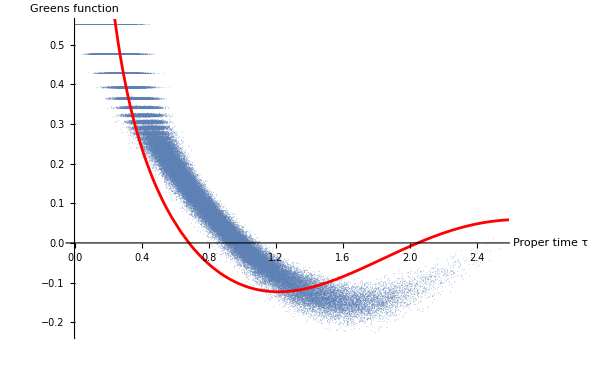
```mathematica
-Graphics-n=2000 (ρ= 337.6)
```

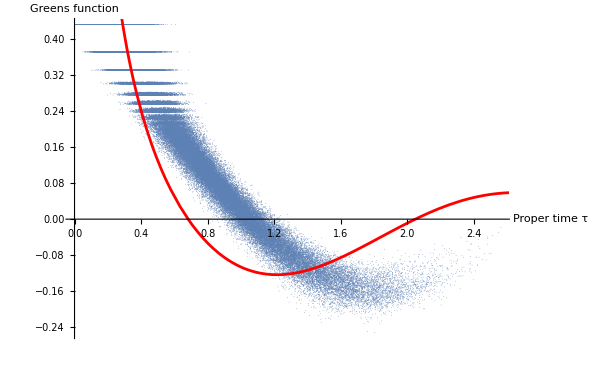
```mathematica
-Graphics-n=1000(ρ= 168.8)
```